```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/With4MOSTErrors/MSTO

```mathematica
<<threeStreamsNearby150k.mx
```

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Define the “true” potential

```mathematica
Phi[r_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])
PhiEff[r_,L_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])+L^2/(2 r^2)
vcirc[r_,M_,b_]:=Sqrt[(M r^2)/(Sqrt[b^2+r^2] (b+Sqrt[b^2+r^2])^2)]
```

```mathematica
Jr[r_,pr_,L_,M_,b_]:=M/Sqrt[-pr^2-L^2/r^2+2 M/(b+Sqrt[b^2+r^2])]-1/2 (L+Sqrt[L^2+4 M b]/2)
```

Color point plots

```mathematica
ListColorPlot[x_,y_,c_,csize_,cscl_,xlab_,ylab_]:=Show[Graphics[Flatten[MapThread[{ColorData[cscl][(#3-Min[c])/(Max[c]-Min[c])],Disk[{#1,#2},csize]}&,{x,y,c}]]],Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],FrameLabel->{xlab,ylab}]
```

Annotation for the color plot - shows a color bar

```mathematica
PlotAnnotate[M_,b_,crange_,dc_,label_]:=Graphics[{Style[Text["M = "<>ToString[M]<>" \!\(\*SuperscriptBox[\(kpc\), \(3\)]\)\!\(\*SuperscriptBox[\(Myr\), \(-2\)]\), b="<>ToString[b]<>" kpc",Scaled[{0.02,0.98}],{-1,1}],TextAlignment->-1,FontFamily->"Helvetica",FontSize->18],MyColorBar[crange,dc,label][[1]]}]

α=0.9;(*total scaled width of color bar*)
β=0.05;(*scaled offset from the left end of the plot*)
γ=0.05;(*scaled distance of the bottom of the bar from the bottom of the plot*)
δγ=0.03;(*scaled height of color bar*)MyColorBar[crange_,dc_,label_]:=Graphics[Flatten[{Black,Style[Text[label,Scaled[{β/2,γ+δγ/2}]],FontFamily->"Helvetica",FontSize->14],Table[{ColorData["Rainbow"][(c-crange[[1]])/(crange[[2]]-crange[[1]])],Rectangle[Scaled[{α (c-crange[[1]])/(crange[[2]]+dc-crange[[1]])+β,γ}],Scaled[{α (c-crange[[1]]+dc)/(crange[[2]]+dc-crange[[1]])+β,γ+δγ}]],Black,Style[Text[Round[c,dc],Scaled[{α (c-crange[[1]]+dc/2)/(crange[[2]]+dc-crange[[1]])+β,γ+1.75 δγ}]],FontFamily->"Helvetica",FontSize->14]},{c,crange[[1]],crange[[2]],dc}]}]]
```

```mathematica
MyColorBar[{0,10},1,"J_r"]
```

-Graphics-

Examine distances from the Sun to the stream stars

```mathematica
trueDists=Sqrt[(truePositions[[All,1]]-8)^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

```mathematica
dbins=Table[id,{id,0,80,1}];
dcounts=BinCounts[trueDists,{dbins}];
```

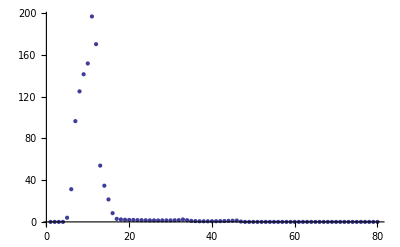

```mathematica
ListPlot[Transpose[{dbins[[2;;Length[dbins]]],dcounts/(dbins[[2;;Length[dbins]]]^2)}],PlotRange->All]
```

Convert (x,v) to observables, convolve with errors, and convert back to (x’,v’)

NOTE: make sure that these four filenames are the same in here and in data_realization_gaia.f!!!!

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
```

OutputStream[pos.test.dat,45]

OutputStream[vel.test.dat,46]

```mathematica
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.test.dat

vel.test.dat

## At this point, manually run data_realizations_gaia

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

150000

150000

{150000,3}

{150000,3}

{150000,11}

columns of observational file are vmag, alpha, delta, parallax, par error, mu_alpha, pm error, mu_delta, pm error, RV, RV error

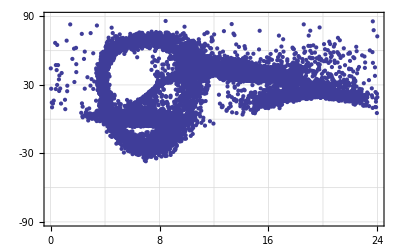

```mathematica
ListPlot[Transpose[{convObs[[All,2]]*24/(2π),convObs[[All,3]]/Degree}],PlotRange->{{0,24},{-90,90}},Frame->True,FrameTicks->{Range[0,24,4],Range[-90,90,30],None,None},GridLines->{Range[0,24,4],Range[-90,90,30]}]
```

Data quality cuts (on observational data)

### Histogram of magnitudes - cut out V>20

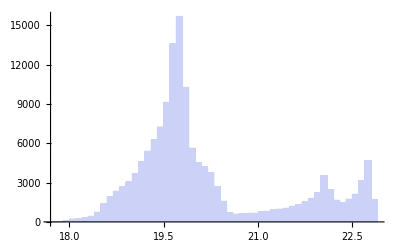

```mathematica
Histogram[convObs[[All,1]]]
```

```mathematica
Tally[magSel=Thread[convObs[[All,1]]<20]]
```

{{False,55030},{True,94970}}

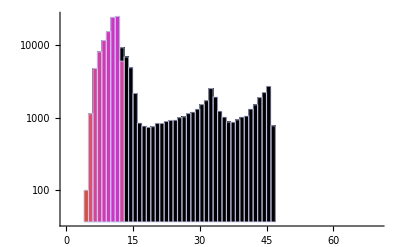

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Cut out negative parallaxes, and those with huge errors

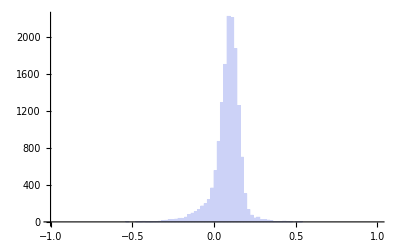

```mathematica
Histogram[convObs[[All,4]],{-1,1,.02}]
```

```mathematica
Tally[posParSel=Thread[Thread[(convObs[[All,4]]>1*^-5)]&&Thread[(convObs[[All,4]]<10)]]]
```

{{False,83021},{True,66979}}

```mathematica
pars=Pick[convObs[[All,4]],posParSel];
```

```mathematica
pars[[Ordering[pars,-50]]]
```

{0.327938,0.327994,0.329857,0.330701,0.33088,0.331679,0.331911,0.335652,0.339211,0.339416,0.339823,0.340028,0.340075,0.340311,0.342495,0.34381,0.345082,0.345452,0.345637,0.347707,0.348615,0.350775,0.353424,0.355302,0.357447,0.363481,0.375603,0.377096,0.381029,0.385461,0.394306,0.400723,0.406589,0.416263,0.422559,0.430812,0.432041,0.434853,0.438074,0.438484,0.438963,0.443473,0.443565,0.445678,0.456237,0.470945,0.470957,0.500257,0.506588,0.524528}

Histogram::hbins: The bin specification {"Log", {-5, 0, 0.1}} cannot be used to determine either how many or which bins to use.

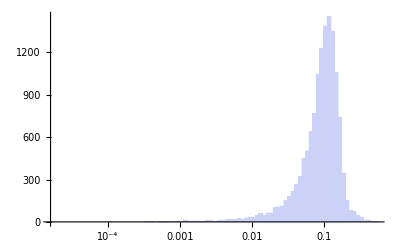

```mathematica
Histogram[Pick[convObs[[All,4]],posParSel],{"Log",{-5,0,0.1}}]
```

```mathematica
Tally[hugeParErrSel=Thread[Abs[convObs[[All,5]]]< 1000]]
```

{{False,55030},{True,94970}}

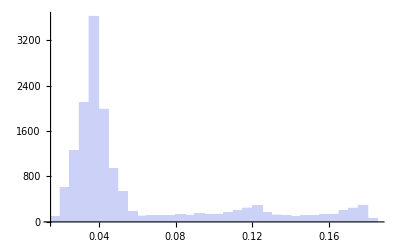

```mathematica
Histogram[Pick[convObs[[All,5]],hugeParErrSel],PlotRange->All]
```

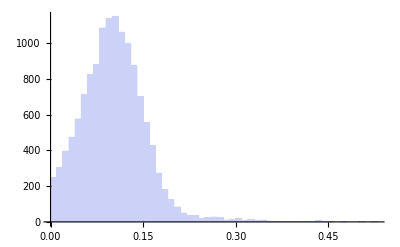

```mathematica
Histogram[Pick[convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],PlotRange->All]
```

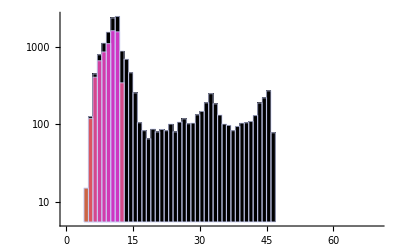

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

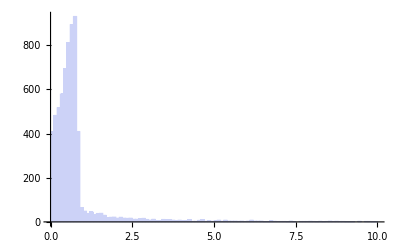

```mathematica
Histogram[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],{0,10,0.1}]
```

```mathematica
Log10[Max[trueDists]]
```

1.66719

```mathematica
Log10[Min[trueDists]]
```

0.653211

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

-4.25026

```mathematica
Max[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

3.21689

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]],1,"Rainbow","RA","Dec"],MyColorBar[{-4.25,3.25},0.25,"σ_D/D"]]
```

-Graphics-

```mathematica
Log10[Min[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

-1.15366

```mathematica
Log10[Max[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

3.95239

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{-1.15,4.0},0.5,"σ_π/π"]]
```

-Graphics-

### Dataquality cut on parallaxes

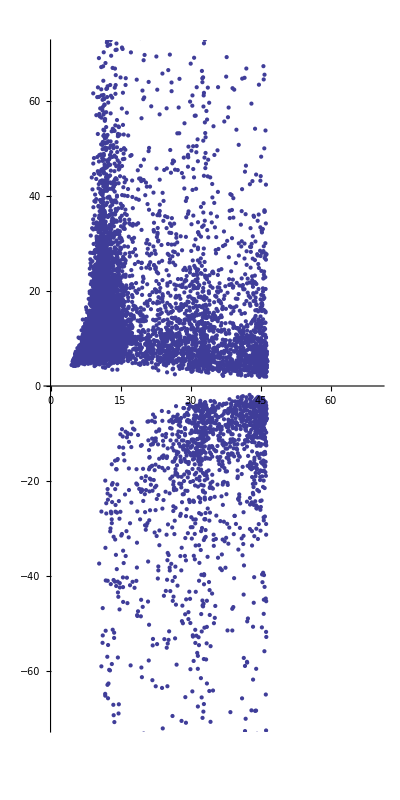

```mathematica
ListPlot[Transpose[{trueDists,1/convObs[[All,4]]}],PlotRange->{{0,70},{-70,70}},AspectRatio->2]
```

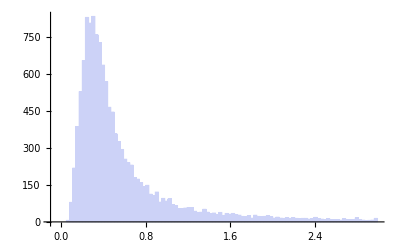

```mathematica
Histogram[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]],{-.1,3,.03}]
```

```mathematica
Tally[dqParSel=Thread[Abs[convObs[[All,5]]/convObs[[All,4]]]<0.3]]
```

{{False,149507},{True,493}}

```mathematica
Dimensions[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]
```

{439}

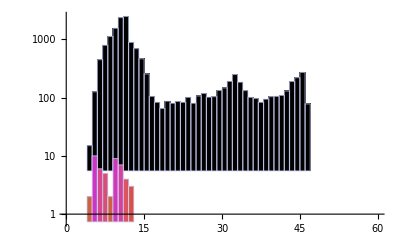

```mathematica
Show[Histogram[trueDists,{0,60,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]],{0,60,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.32703

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.06942

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.686973

```mathematica
Max[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.09473

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.7,1.1},0.1,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.32703

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.06942

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.3,1.1},0.1,"[1/π]"]]
```

-Graphics-

### Dataquality cut on proper motions is basically the same as for pars - errors are proportional

### Dataquality cut on RVs

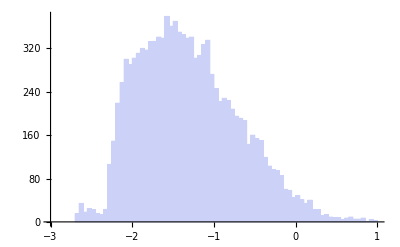

```mathematica
Histogram[Log10[convObs[[All,11]]/convObs[[All,10]]],{-3,1,.05}]
```

```mathematica
Tally[dqRVSel=Thread[Abs[convObs[[All,11]]/convObs[[All,10]]]<0.3]]
```

{{False,60999},{True,89001}}

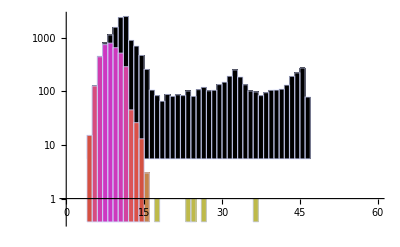

```mathematica
Show[Histogram[trueDists,{0,60,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]],{0,60,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Combining all the cuts together

```mathematica
Tally[allSels=Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]]
```

{{False,149577},{True,423}}

```mathematica
Dimensions[tpSel=Pick[truePositions,allSels]]
```

{170,3}

```mathematica
Dimensions[cpSel=Pick[convPositions,allSels]]
```

{170,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,allSels]]
```

{170,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,allSels]]
```

{170,3}

```mathematica
Tally[Thread[allSels&&s1sel]]
```

{{False,149939},{True,61}}

```mathematica
Tally[Thread[allSels&&s2sel]]
```

{{False,149917},{True,83}}

```mathematica
Tally[Thread[allSels&&s3sel]]
```

{{False,149974},{True,26}}

```mathematica
Dimensions[tpSel1=Pick[truePositions,Thread[allSels&&s1sel]]]
```

{61,3}

```mathematica
Dimensions[cpSel1=Pick[convPositions,Thread[allSels&&s1sel]]]
```

{61,3}

```mathematica
Dimensions[tvSel1=Pick[trueVelocities,Thread[allSels&&s1sel]]]
```

{61,3}

```mathematica
Dimensions[cvSel1=Pick[convVelocities,Thread[allSels&&s1sel]]]
```

{61,3}

```mathematica
Dimensions[tpSel2=Pick[truePositions,Thread[allSels&&s2sel]]]
```

{83,3}

```mathematica
Dimensions[cpSel2=Pick[convPositions,Thread[allSels&&s2sel]]]
```

{83,3}

```mathematica
Dimensions[tvSel2=Pick[trueVelocities,Thread[allSels&&s2sel]]]
```

{83,3}

```mathematica
Dimensions[cvSel2=Pick[convVelocities,Thread[allSels&&s2sel]]]
```

{83,3}

```mathematica
Dimensions[tpSel3=Pick[truePositions,Thread[allSels&&s3sel]]]
```

{26,3}

```mathematica
Dimensions[cpSel3=Pick[convPositions,Thread[allSels&&s3sel]]]
```

{26,3}

```mathematica
Dimensions[tvSel3=Pick[trueVelocities,Thread[allSels&&s3sel]]]
```

{26,3}

```mathematica
Dimensions[cvSel3=Pick[convVelocities,Thread[allSels&&s3sel]]]
```

{26,3}

### Plots examining error behavior etc

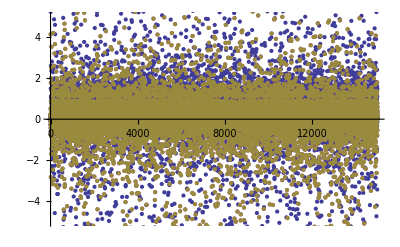

```mathematica
ListPlot[Transpose[(truePositions-convPositions)/truePositions],PlotRange->{-5,5}]
```

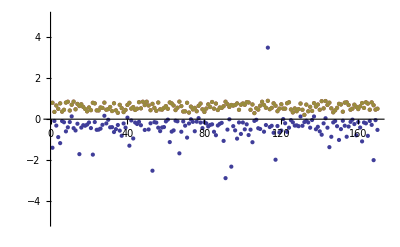

```mathematica
ListPlot[Transpose[(tpSel-cpSel)/tpSel],PlotRange->{-5,5}]
```

```mathematica
convDists=Sqrt[(convPositions[[All,1]]-8)^2+convPositions[[All,2]]^2+convPositions[[All,3]]^2];
```

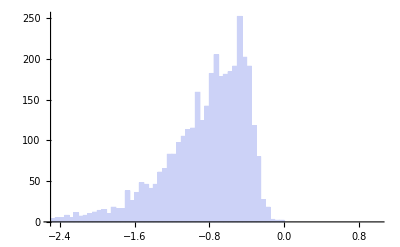

```mathematica
Histogram[Pick[Log10[Abs[(trueDists-convDists)]/trueDists],allSels],{-2.5,1,0.05}]
```

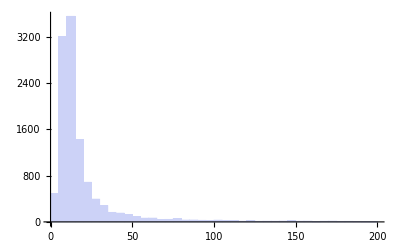

```mathematica
Histogram[Pick[convDists,Thread[!allSels]],{0,200,5}]
```

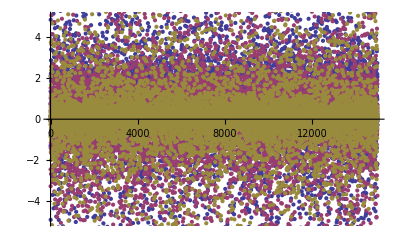

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

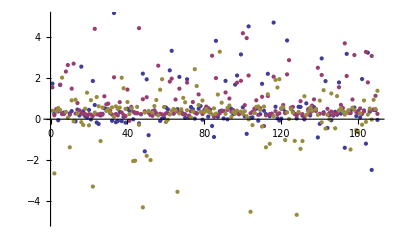

```mathematica
ListPlot[Transpose[(tvSel-cvSel)/tvSel],PlotRange->{-5,5}]
```

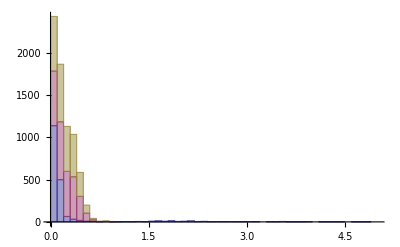

```mathematica
Histogram[Transpose[(tpSel-cpSel)/tpSel],{0,5,.1},ChartLayout->"Stacked"]
```

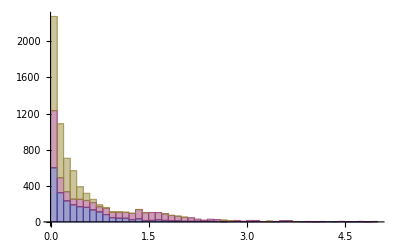

```mathematica
Histogram[Transpose[(tvSel-cvSel)/tvSel],{0,5,.1},ChartLayout->"Stacked"]
```

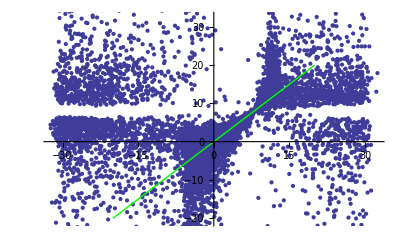

```mathematica
Show[ListPlot[Transpose[{truePositions[[All,1]],convPositions[[All,1]]}]],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

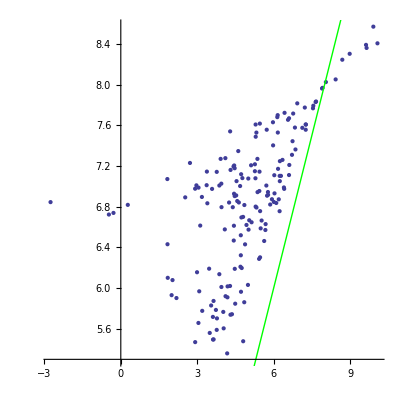

```mathematica
Show[ListPlot[Transpose[{tpSel[[All,1]],cpSel[[All,1]]}],AspectRatio->1],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

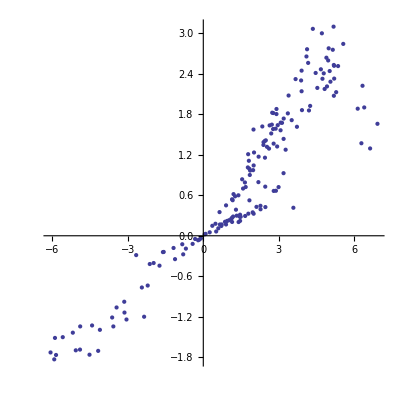

```mathematica
ListPlot[Transpose[{tpSel[[All,2]],cpSel[[All,2]]}],AspectRatio->1]
```

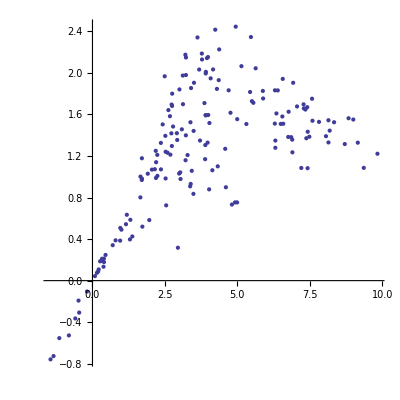

```mathematica
ListPlot[Transpose[{tpSel[[All,3]],cpSel[[All,3]]}],AspectRatio->1]
```

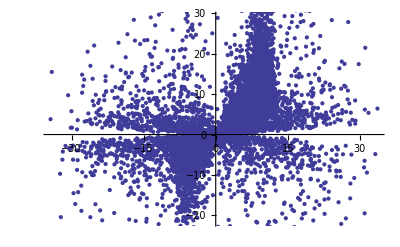

```mathematica
ListPlot[Transpose[{truePositions[[All,3]],convPositions[[All,3]]}]]
```

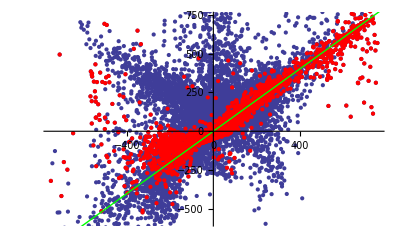

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,1]],convVelocities[[All,1]]}]],ListPlot[Transpose[{tvSel[[All,1]],cvSel[[All,1]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

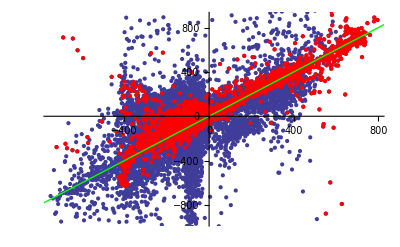

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,2]],convVelocities[[All,2]]}]],ListPlot[Transpose[{tvSel[[All,2]],cvSel[[All,2]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

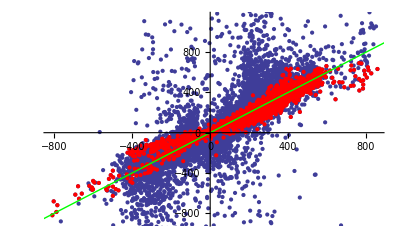

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,3]],convVelocities[[All,3]]}]],ListPlot[Transpose[{tvSel[[All,3]],cvSel[[All,3]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

Convert (x’,v’) to (Jr’,L’,Lz’)

```mathematica
fnameCleanPosIn="pos.clean.dat"
fnameCleanVelIn="vel.clean.dat"
```

pos.clean.dat

vel.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[pos.clean.dat,81]

OutputStream[vel.clean.dat,82]

```mathematica
Write[pStream,Length[cpSel]];
Export[pStream,cpSel,"Data"];
Export[vStream,cvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.clean.dat

vel.clean.dat

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,5065,8]

```mathematica
Mtrial=12.2;
btrial=8.0;
```

```mathematica
Dimensions[convJ=Table[{0,0,0},{i,1,Length[cpSel]}]]
Dimensions[convJ1=Table[{0,0,0},{i,1,Length[cpSel1]}]]
Dimensions[convJ2=Table[{0,0,0},{i,1,Length[cpSel2]}]]
Dimensions[convJ3=Table[{0,0,0},{i,1,Length[cpSel3]}]]
```

{170,3}

{61,3}

{83,3}

{26,3}

```mathematica
For[i=1,i≤Length[cpSel],i++,convJ[[i]]=CartToAA[Mtrial,btrial,cpSel[[i]],cvSel[[i]]];];
For[i=1,i≤Length[cpSel1],i++,convJ1[[i]]=CartToAA[Mtrial,btrial,cpSel1[[i]],cvSel1[[i]]];];
For[i=1,i≤Length[cpSel2],i++,convJ2[[i]]=CartToAA[Mtrial,btrial,cpSel2[[i]],cvSel2[[i]]];];
For[i=1,i≤Length[cpSel3],i++,convJ3[[i]]=CartToAA[Mtrial,btrial,cpSel3[[i]],cvSel3[[i]]];];
```

Some stuff has unbound orbits, so select those out

```mathematica
Tally[boundSel=Thread[convJ[[All,3]]!=0]]
```

{{True,170}}

```mathematica
Dimensions[convJbound=Pick[convJ,boundSel]]
```

{170,3}

```mathematica
Dimensions[tJSel=Pick[Pick[trueActions,allSels],boundSel]]
```

{170,3}

```mathematica
Dimensions[tJSel1=Pick[trueActions,Thread[allSels&&s1sel]]]
```

{61,3}

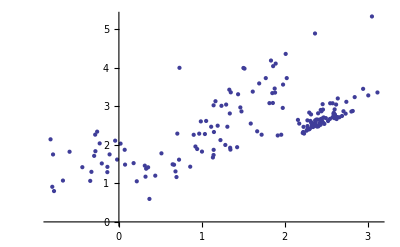

```mathematica
ListPlot[convJbound[[All,{1,2}]]]
```

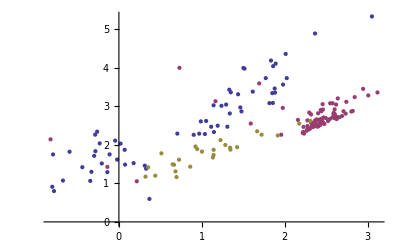

```mathematica
ListPlot[{convJ1[[All,{1,2}]],convJ2[[All,{1,2}]],convJ3[[All,{1,2}]]}]
```

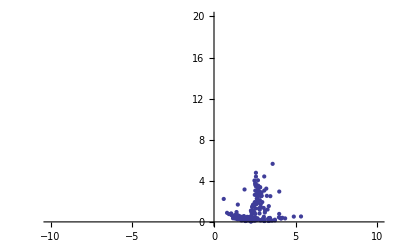

```mathematica
ListPlot[convJbound[[All,{2,3}]],PlotRange->{{-10,10},{0,20}}]
```

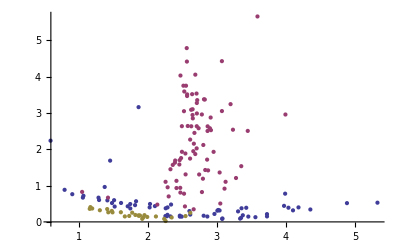

```mathematica
ListPlot[{convJ1[[All,{2,3}]],convJ2[[All,{2,3}]],convJ3[[All,{2,3}]]}]
```

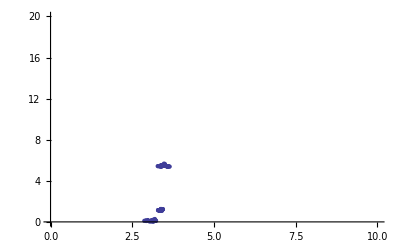

```mathematica
ListPlot[tJSel[[All,{2,3}]],PlotRange->{{0,10},{0,20}}]
```

```mathematica
ListPointPlot3D[convJbound]
```

-Graphics3D-

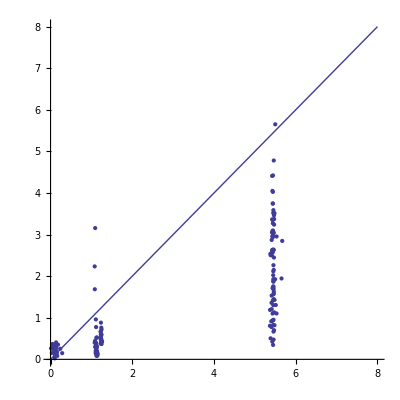

```mathematica
Show[ListPlot[Transpose[{tJSel[[All,3]],convJbound[[All,3]]}],PlotRange->{{0,8},{0,8}},AspectRatio->1],Plot[x,{x,0,8}]]
```

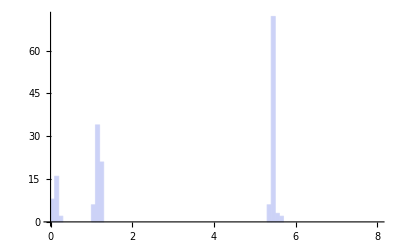

```mathematica
Histogram[tJSel[[All,3]],{0,8,.1}]
```

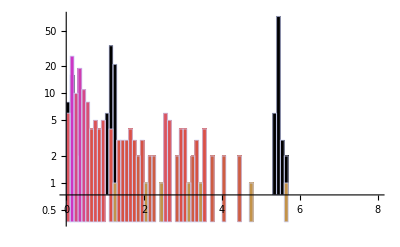

```mathematica
Show[Histogram[tJSel[[All,3]],{0,8,.1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[convJbound[[All,3]],{0,8,.1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

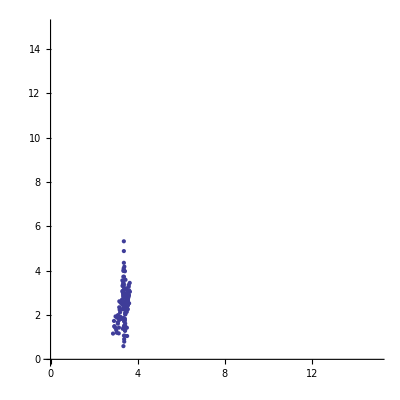

```mathematica
ListPlot[Transpose[{tJSel[[All,2]],convJbound[[All,2]]}],PlotRange->{{0,15},{0,15}},AspectRatio->1]
```

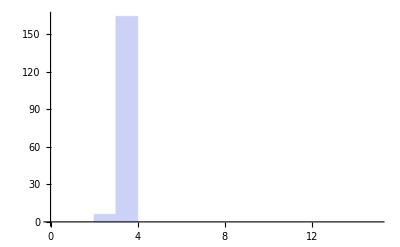

```mathematica
Histogram[tJSel[[All,2]],{0,15,1}]
```

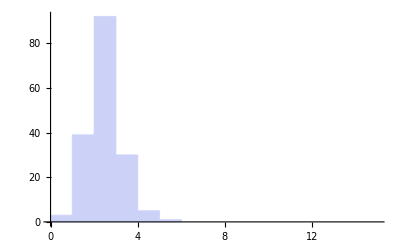

```mathematica
Histogram[convJbound[[All,2]],{0,15,1}]
```

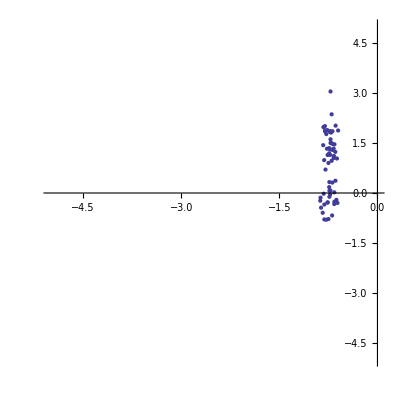

```mathematica
ListPlot[Transpose[{tJSel[[All,1]],convJbound[[All,1]]}],PlotRange->{{-5,0},{-5,5}},AspectRatio->1]
```

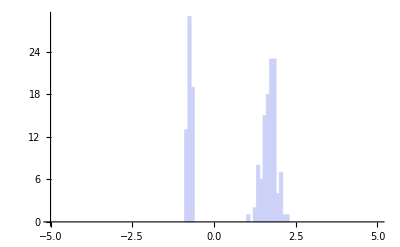

```mathematica
Histogram[tJSel[[All,1]],{-5,5,.1}]
```

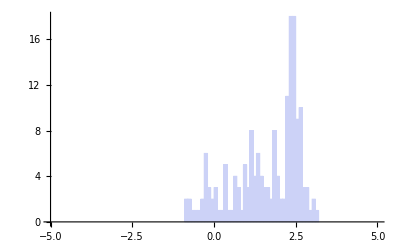

```mathematica
Histogram[convJbound[[All,1]],{-5,5,.1}]
```